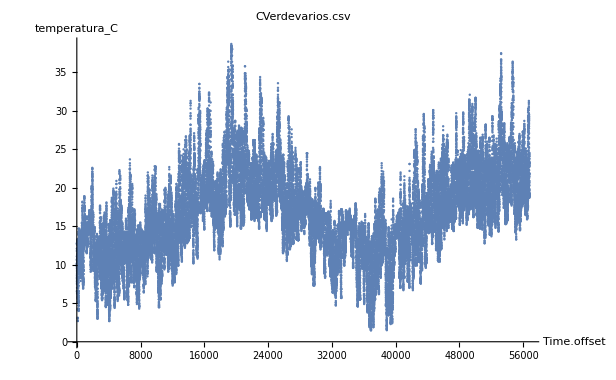

TemporalData::rsmplng: The data is not uniformly spaced and will be automatically resampled to the resolution of the minimum time increment.

ARMAProcess[0.086594,{1.00349,0.168218,-0.0535437,0.15163,-0.275089},{0.558753,0.140388,0.0466779,-0.105968,-0.0236533},0.0536032]

Piecewise[{{31.4813, Abs[s-t]==0}, {34.838 1.01377^(-1-Abs[s-t])-3.36876 1.1691^(-1-Abs[s-t])+0.000376557 (-1)^Abs[s-t] 1.37953^(-1-Abs[s-t])+0.00348773 0.670653^Abs[s-t] Cos[0.805939-1.65545 Abs[s-t]], True}}]

23.284

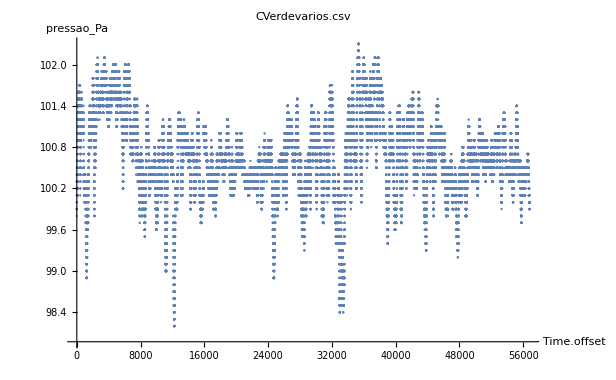

TemporalData::rsmplng: The data is not uniformly spaced and will be automatically resampled to the resolution of the minimum time increment.

SARIMAProcess[3.16201×10^-6,{},0,{0.044146,-0.0548433},{1,{},1,{}},0.000694341]

Piecewise[{{0.000697783, s==0&&t==0}, {0.000726754, s==0&&t==1}, {0.000688674, s==0&&t==2}, {-0.00003808 (1+Min[0,-2+t])+0.0000289713 (1+Min[0,-1+t])+0.000697783 (1+Min[0,t]), s==0&&t>2}, {0.000726754, s==1&&t==0}, {0.00145351, s==1&&t==1}, {0.0014444, s==1&&t==2}, {-0.00003808 (1+Min[1,-2+t])+0.0000289713 (1+Min[1,-1+t])+0.000697783 (1+Min[1,t])+0.0000289713 Min[1,1+t], s==1&&t>2}, {0.000688674, s==2&&t==0}, {0.0014444, s==2&&t==1}, {0.00213307, s==2&&t==2}, {-0.00003808 (1+Min[2,-2+t])+0.0000289713 (1+Min[2,-1+t])+0.000697783 (1+Min[2,t])+0.0000289713 Min[2,1+t]-0.00003808 (-1+Min[2,2+t]), s==2&&t>2}, {0.000697783 (1+Min[0,s])+0.0000289713 Min[1,s]-0.00003808 (-1+Min[2,s]), s>2&&t==0}, {0.0000289713 (1+Min[0,s])+0.000697783 (1+Min[1,s])+0.0000289713 Min[2,s]-0.00003808 (-1+Min[3,s]), s>2&&t==1}, {-0.00003808 (1+Min[0,s])+0.0000289713 (1+Min[1,s])+0.000697783 (1+Min[2,s])+0.0000289713 Min[3,s]-0.00003808 (-1+Min[4,s]), s>2&&t==2}, {-0.00003808 (1+Min[s,-2+t])+0.0000289713 (1+Min[s,-1+t])+0.000697783 (1+Min[s,t])+0.0000289713 Min[s,1+t]-0.00003808 (-1+Min[s,2+t]), s>2&&t>2}, {0, True}}]

100.

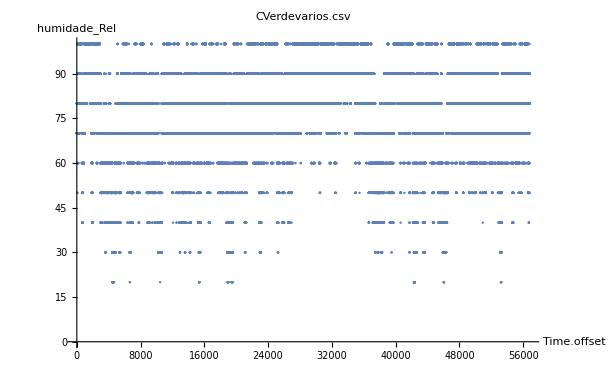

TemporalData::rsmplng: The data is not uniformly spaced and will be automatically resampled to the resolution of the minimum time increment.

ARMAProcess[1.01129,{0.882654,0.0179338,0.0864192},{0.141348,0.0582208},6.73326]

Piecewise[{{314.173, Abs[s-t]==0}, {317.48 1.011^(-1-Abs[s-t])+0.640361 0.295584^Abs[s-t] Cos[1.33708-1.75187 Abs[s-t]], True}}]

79.9525

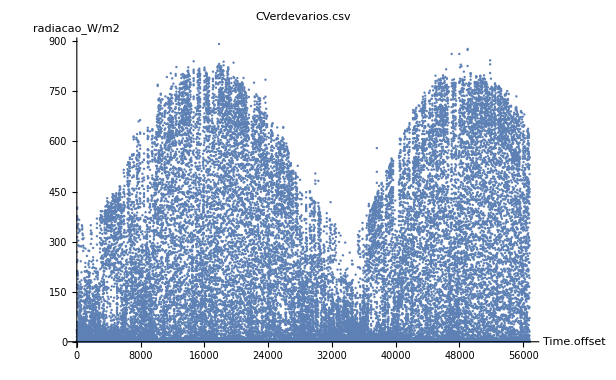

TemporalData::rsmplng: The data is not uniformly spaced and will be automatically resampled to the resolution of the minimum time increment.

ARMAProcess[2.64978,{0.981721},{0.123769},1318.26]

Piecewise[{{46816.2 1.01862^(-1-Abs[s-t]), Abs[s-t]>0}, {45794.2, True}}]

537.754

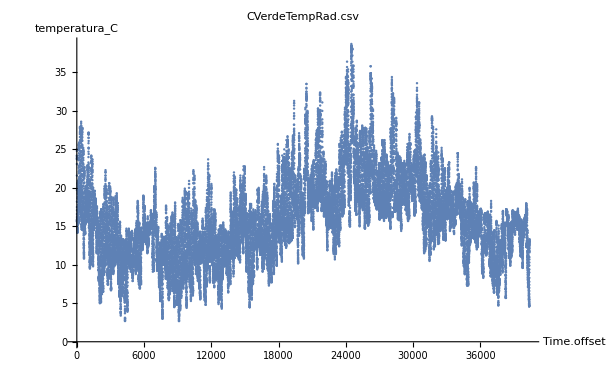

TemporalData::rsmplng: The data is not uniformly spaced and will be automatically resampled to the resolution of the minimum time increment.

ARIMAProcess[-3.0798×10^-6,{0.92406},1,{-0.117121},0.000337919]

CovarianceFunction[ARIMAProcess[-3.0798×10^-6,{0.92406},1,{-0.117121},0.000337919],s,t]

11.2589

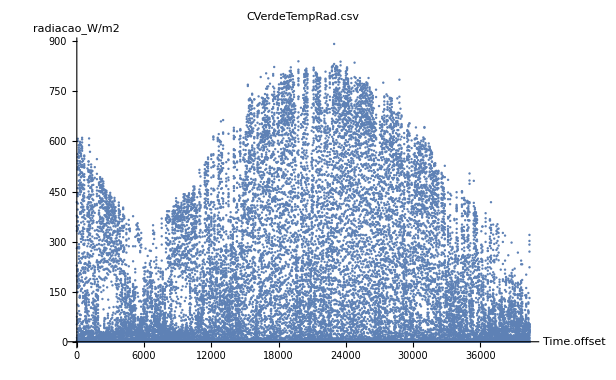

TemporalData::rsmplng: The data is not uniformly spaced and will be automatically resampled to the resolution of the minimum time increment.

ARMAProcess[0.0904852,{1.83059,-0.831316},{0.0821862,0.0977785},7.65526]

Piecewise[{{44548.6 1.00445^(-1-Abs[s-t])-1314.59 1.19759^(-1-Abs[s-t]), Abs[s-t]>0}, {43254.6, True}}]

-4.499

```mathematica
ClearAll["Global`*"]

fitTimeseriesModel[f_,y_,z_]:=Module[{fname=f,yaxis=y,colnum=z},
dataset=Import[StringJoin["/home/david/Documents/digital-twins/d4fa/HistoriMeteo/",fname],{"CSV","Data",All,{1,z}},"HeaderLines"->1,"FieldSeparators"->",",MissingDataRules->{"."->Missing[],""->Missing[]}];
time=dataset[[All,1]];
time=Subtract[time,time[[1]]];
timeseries=TimeSeries[dataset[[All,2]],{time}]; (* is 2 because only 2 data columns read *)
Print[ListPlot[dataset[[All,2]],PlotLabel->fname,AxesLabel->{"Time.offset",yaxis}]];
atsm=TimeSeriesModelFit[timeseries];
process=Normal[atsm];
Print[process];
Print[CovarianceFunction[process,s,t]];
Print[TimeSeriesForecast[process,dataset[[All,2]], 2]];
];
(***********************************************)
 (* utc_timestamp, temperatura_C, pressao_Pa, humidade_Rel, radiacao_W/m2 *)
 fitTimeseriesModel["CVerdevarios.csv","temperatura_C",2]; 
fitTimeseriesModel["CVerdevarios.csv","pressao_Pa",3];
fitTimeseriesModel["CVerdevarios.csv","humidade_Rel",4];
fitTimeseriesModel["CVerdevarios.csv","radiacao_W/m2",5];

(* utc_timestamp, temperatura_C, radiacao *)
 fitTimeseriesModel["CVerdeTempRad.csv","temperatura_C", 2];  
fitTimeseriesModel["CVerdeTempRad.csv","radiacao_W/m2", 3]; 
(***********************************************)
```